```mathematica
NDSolve[{x1'[t]-10(x2[t]-x1[t])==0,x2'[t]+x1[t]x3[t]-28x1[t]+x2[t]==0,x3'[t]-x1[t]x2[t]+8x3[t]/3==0,x1[0]==2,x2[0]==2,x3[0]==10},{x1,x2,x3},{t,0,50}]
```

{{x1→InterpolatingFunction[…],x2→InterpolatingFunction[…],x3→InterpolatingFunction[…]}}

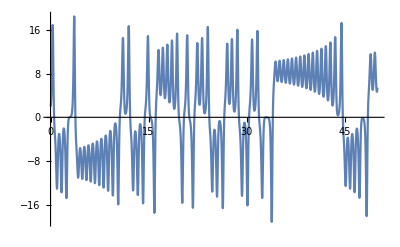

```mathematica
{{x1->InterpolatingFunction[…],x2->InterpolatingFunction[…],x3->InterpolatingFunction[…]}}
Plot[Evaluate[x1[t]/.%1],{t,0,50}]
```